```mathematica
GraphData["GrotzschGraph","Spectrum"]
```

{1/2 (1-√41),1/2 (-3-√5),1/2 (-3-√5),1/2 (-3+√5),1/2 (-3+√5),1,1,1,1,1,1/2 (1+√41)}

```mathematica
GraphData[]
```

```mathematica
SolsFour[g_]:=Block[{sols,four},
sols=FindFullFormula[g];
four=Select[sols,2<=StringCount[SymbolName[#],"x"]<3&];
Sort[four]
]
```

```mathematica
ExamineGraph [Graph[GraphData["GrotzschGraph"],VertexLabels->"Name"]]
```

Interrupted

```mathematica
BellB[11]
```

678570

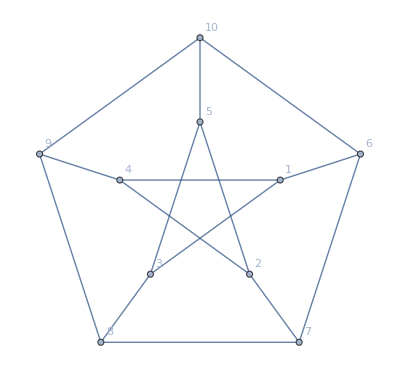
{-Graphics-→{20,0,540,128a♁346♁579 | 129♁347a♁568 | 1579♁268♁34a | 159♁268♁347a
128a♁347♁569 | 129♁37a♁4568 | 1579♁28a♁346 | 179♁23a♁4568
128a♁369♁457 | 12a♁379♁4568 | 157♁2369♁48a | 17a♁2369♁458
128a♁379♁456 | 1579♁236♁48a | 158♁2369♁47a | 17a♁239♁4568
128♁347a♁569 | 1579♁23a♁468 | 158♁269♁347a | 18a♁2369♁457},1<->3→{8,0,732,1239♁4568♁7a | 123a♁4568♁79 | 1379♁28a♁456 | 137a♁269♁458
1239♁47a♁568 | 123a♁468♁579 | 1379♁2a♁4568 | 137a♁29♁4568},1<->4→{8,0,732,1457♁2369♁8a | 1458♁2369♁7a | 147a♁2369♁58 | 148a♁2369♁57
1457♁28a♁369 | 1458♁269♁37a | 147a♁239♁568 | 148a♁236♁579},1<->6→{8,0,732,1268♁347a♁59 | 1269♁347a♁58 | 1568♁239♁47a | 1569♁28a♁347
1268♁34a♁579 | 1269♁37a♁458 | 1568♁29♁347a | 1569♁28♁347a},2<->4→{8,0,732,1579♁2346♁8a | 1579♁2468♁3a | 157♁248a♁369 | 179♁234a♁568
1579♁234a♁68 | 1579♁248a♁36 | 159♁2468♁37a | 18a♁2346♁579},2<->5→{8,0,732,1258♁347a♁69 | 1259♁347a♁68 | 179♁2568♁34a | 18♁2569♁347a
1258♁369♁47a | 1259♁37a♁468 | 18a♁2569♁347 | 19♁2568♁347a},2<->7→{8,0,732,1279♁34a♁568 | 127a♁369♁458 | 159♁237a♁468 | 19♁237a♁4568
1279♁3a♁4568 | 127a♁39♁4568 | 18a♁2379♁456 | 1a♁2379♁4568},3<->5→{8,0,732,128a♁3456♁79 | 128a♁3569♁47 | 128♁3569♁47a | 179♁28a♁3456
128a♁3457♁69 | 128a♁3579♁46 | 12a♁3579♁468 | 18a♁269♁3457},3<->8→{8,0,732,12a♁3468♁579 | 1579♁238a♁46 | 1579♁2a♁3468 | 159♁2368♁47a
1579♁2368♁4a | 1579♁26♁348a | 157♁269♁348a | 179♁238a♁456},4<->9→{8,0,732,128a♁3469♁57 | 128a♁36♁4579 | 128♁37a♁4569 | 157♁28a♁3469
128a♁3479♁56 | 128a♁37♁4569 | 12a♁3479♁568 | 18a♁236♁4579},5<->10→{8,0,732,128♁369♁457a | 157a♁239♁468 | 158a♁269♁347 | 17♁2369♁458a
157a♁2369♁48 | 158a♁2369♁47 | 179♁236♁458a | 18♁2369♁457a},6<->7→{8,0,732,128a♁3467♁59 | 128a♁3679♁45 | 128♁34a♁5679 | 159♁28a♁3467
128a♁34♁5679 | 128a♁39♁4567 | 12a♁3679♁458 | 18a♁239♁4567},6<->10→{8,0,732,128♁346a♁579 | 1579♁23♁468a | 1579♁28♁346a | 159♁268a♁347
1579♁236a♁48 | 1579♁268a♁34 | 157♁239♁468a | 179♁236a♁458},7<->8→{8,0,732,12a♁369♁4578 | 1578♁269♁34a | 15♁2369♁478a | 178a♁239♁456
1578♁2369♁4a | 159♁236♁478a | 178a♁2369♁45 | 1a♁2369♁4578},8<->9→{8,0,732,1289♁347a♁56 | 12a♁347♁5689 | 157♁2689♁34a | 1589♁26♁347a
1289♁37a♁456 | 12♁347a♁5689 | 1589♁236♁47a | 15♁2689♁347a},9<->10→{8,0,732,128♁379a♁456 | 129a♁37♁4568 | 157♁239a♁468 | 179a♁23♁4568
129a♁347♁568 | 12♁379a♁4568 | 179a♁236♁458 | 17♁239a♁4568}}

```mathematica
ExamineGraph [Graph[PetersenGraph[],VertexLabels->"Name"]]
```